```mathematica
Quit
```

## Init

Load the package and set the base directory where intermediate files will be created:

```mathematica
AppendTo[$Path,ParentDirectory@NotebookDirectory[]];
Needs["AstronomicalDiaries`"]
```

```mathematica
$ADBase=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Data"}];
```

## Observations

```mathematica
observations=ADObservations[];
```

```mathematica
modelObservations=Select[observations,!#Damaged&&!MissingQ[#Object]&&!MissingQ[#Reference]&&!MissingQ[#Date]&&!MissingQ[#Relation]&&!(MissingQ[#Cubits]&&MissingQ[#Fingers])&];
```

## Testing

```mathematica
Needs["AstronomicalDiaries`Modeling`"]
```

```mathematica
Get["AstronomicalDiaries`Modeling`"]
```

```mathematica
chains=Table[EchoTiming@fitModel[modelObservations[[;;10]],1000,1,{"p","m","muTimes","sigma2Times","t","timeCats","l","sigma2","muOutlier","sigma2Outlier","deltaD","months","years"},False],4];
```

$Aborted

```mathematica
gewekeObservations=RandomSample[modelObservations,10];
```

```mathematica
gewekeObservations=modelObservations[[;;10]];
```

```mathematica
gewekeChain=fitModel[gewekeObservations,10000,20,{"p","m","muTimes","sigma2Times","t","timeCats","l","sigma2","muOutlier","sigma2Outlier","deltaD","months","years"},True][[500;;;;10]];
```

General::munfl: Exp[-800.903] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1184.78] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3353.72] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

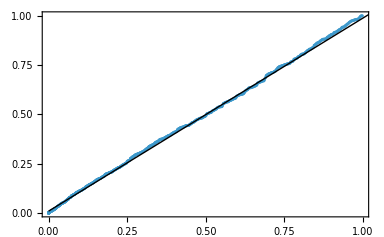

```mathematica
QuantilePlot[gewekeChain[[All,"p"]],AstronomicalDiaries`Modeling`Private`pPrior[],PlotRange->All]
```

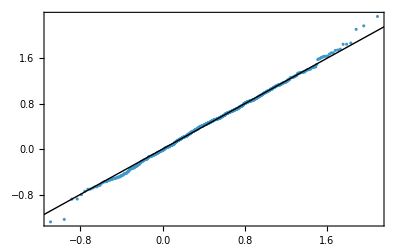

```mathematica
QuantilePlot[gewekeChain[[All,"l"]],AstronomicalDiaries`Modeling`Private`lPrior[],PlotRange->All]
```

```mathematica
AstronomicalDiaries`Modeling`Private`muTimesPrior[{"LastPartOfTheNight"}][[1]]
```

NormalDistribution[0,6]

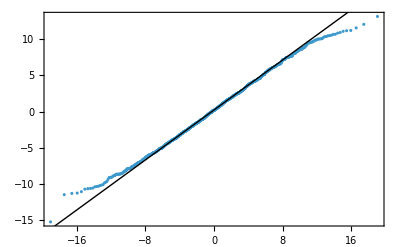

```mathematica
QuantilePlot[gewekeChain[[All,"muTimes","LastPartOfTheNight"]],AstronomicalDiaries`Modeling`Private`muTimesPrior[{"LastPartOfTheNight"}][[1]],PlotRange->All]
```

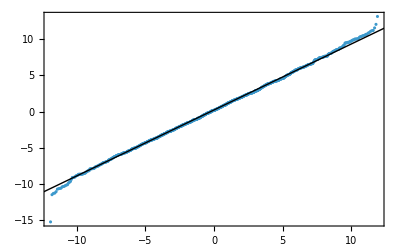

```mathematica
QuantilePlot[gewekeChain[[All,"muTimes","LastPartOfTheNight"]],TruncatedDistribution[{-12,12},AstronomicalDiaries`Modeling`Private`muTimesPrior[{"LastPartOfTheNight"}][[1]]],PlotRange->All]
```

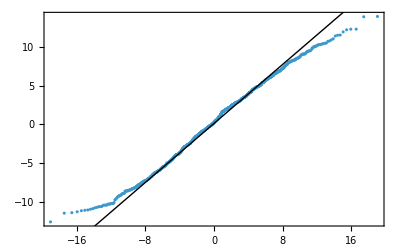

```mathematica
QuantilePlot[gewekeChain[[All,"muTimes","BeginningOfTheNight"]],AstronomicalDiaries`Modeling`Private`muTimesPrior[{"BeginningOfTheNight"}][[1]],PlotRange->All]
```

```mathematica
Keys@gewekeChain[[-1]]
```

{p,m,muTimes,sigma2Times,t,timeCats,l,sigma2,muOutlier,sigma2Outlier,deltaD,months,years}